# Machine Learning Job Classification

## Loading the data

Importing the data file “mindy_els.json”. Normally, a file would be imported using the statement in the comment, but it is being cloud imported for convenience.

```mathematica
jobData = CloudImport[CloudObject[["https://www.wolframcloud.com/obj/anika.karpurapu/Data"](https://www.wolframcloud.com/obj/anika.karpurapu/Data)]](* Import["C:\\Users\\anika\\Downloads\\job_classifier_data_and_reference\\elassandra_backups\\Pipeline_Notebooks\\mindy_els.json", "JSON"] *)
```

{{slug→61362-remote-senior-android-developer-iot-europe-purepoint,id→61362,epoch→1502972704,date→Aug 17, 2017,company→Purepoint,6,timepast→0,tags_display→Dev, Senior, Android, Digital Nomad, Jira, Chrome Os, Computer Architecture, Android, Computing, Smartphones, Agile Software Development, Software, Computing Platforms, Alphabet Inc.,title→title,new→ [New!]},273,{1}}
 |  |  |  |

Exporting the data file to the cloud.

```mathematica
(* CloudExport[jobData, "MX", "Data", Permissions->"Public"] *)
```

Finding the classification for each data point.

```mathematica
labelTypes = Table[jobData[[x]][[11]][[2]], {x, Length[jobData]}];
```

Deleting all the duplicates in the data classifications so that we can find all of the unique labels.

```mathematica
DeleteDuplicates[labelTypes]
```

{Interface Technical Architect,Business Analyst,Software Technical Architect,System Technical Architect,Project Manager,Database Technical Architect,Miscellaneous}

## Splitting the data

Splitting the data into train and test sets using a 80-20 proportion.

```mathematica
{train, test} = (SeedRandom["DataSplit"];ResourceFunction["TrainTestSplit"][jobData])
```

{{{slug→61043-remote-senior-mobile-product-manager-whitespectre,id→61043,epoch→1501160122,date→Jul 27, 2017,company→Whitespectre,6,timepast→21,tags_display→Mobile, Senior, Product Manager, Exec, Project Management, Scrum, Software Development Process, Computing, Management, Mobile App, Agile Software Development, Software,title→title,new→},218,{1}},1}
 |  |  |  |

Checking the length of the training and test sets.

```mathematica
Map[Length,{train, test}]
```

{220,55}

View the 5th data point in the train set.

```mathematica
train[[5]]
```

{slug→60920-remote-product-manager-salehoo-com,id→60920,epoch→1500616200,date→Jul 20, 2017,company→SaleHoo.com,position→Product Manager,tags→{User Experience,Saas,Design,Product Manager,Exec,Digital Nomad,Product Manager,User Experience Design,Product Marketing,Marketing,Human–Computer Interaction,Design,Product Strategy,Business,Web Design,E-Commerce,Economy,Product Management},logo→https://remoteok.io/assets/jobs/5c134dbbe2bb675cf02c3f8bd18fa620.png,description→Doubledot Media (SaleHoo.com's parent company) is a New Zealand-based company creating online eCommerce tools for people looking to start their own online businesses. We're based in Christchurch, but over 95% of our team work remotely from various places around the world. (Living in the future FTW!),url→https://remoteok.io/jobs/60920-remote-product-manager-salehoo-com,label→Business Analyst,timepast→28,tags_display→User Experience, Saas, Design, Product Manager, Exec, Digital Nomad, Product Manager, User Experience Design, Product Marketing, Marketing, Human–Computer Interaction, Design, Product Strategy, Business, Web Design, E-Commerce, Economy, Product Management,title→title,new→}

View the 7th data point in the test set.

```mathematica
test[[7]]
```

{slug→61331-remote-junior-developer-conversio,id→61331,epoch→1502807359,date→Aug 15, 2017,company→Conversio,position→Junior Developer,tags→{Junior,Dev,Digital Nomad},logo→https://we-work-remotely-production.imgix.net/logos/0001/6521/logo.gif,description→The Company,url→https://remoteok.io/jobs/61331-remote-junior-developer-conversio,label→Interface Technical Architect,timepast→2,tags_display→Junior, Dev, Digital Nomad,title→title,new→}

## Testing on the whole dataset

Convert the data to an association, a data structure which is similar to a dictionary.

```mathematica
input = ResourceFunction["ToAssociations"][train]
```

{<|slug→61043-remote-senior-mobile-product-manager-whitespectre,id→61043,epoch→1501160122,date→Jul 27, 2017,company→Whitespectre,6,timepast→21,tags_display→Mobile, Senior, Product Manager, Exec, Project Management, Scrum, Software Development Process, Computing, Management, Mobile App, Agile Software Development, Software,title→title,new→|>,218,<|1|>}
 |  |  |  |

Converts the data into a more organized form.

```mathematica
input = Dataset[input];
```

Run the data through the classifier. We specify a parameter of “input -> ‘label’” because that is the feature we are trying to classify. “label” is the job classification.

```mathematica
classifier = Classify[input -> "label"]
```

ClassifierFunction[…]

Remove the “label” feature from the test set so that we can test the accuracy of the classifier.

```mathematica
testSet = KeyDrop[test, {"label"}];
```

```mathematica
testSet = Dataset[testSet];
```

Running the test set through the classifier

```mathematica
testOutput = classifier[testSet];
```

The real classification for each data point in the test set

```mathematica
realOutput = Table[test[[x]][[11]][[2]], {x, Length[test]}];
```

Abbreviating the outputs for the test set so that it is easier to visualize.

```mathematica
realOutput = StringReplace[realOutput, {"Interface Technical Architect" -> "ITA", "Business Analyst" -> "BA", "System Technical Architect" -> "SyTA", "Software Technical Architect" -> "SoTA", "Project Manager" -> "PM", "Database Technical Architect" -> "DTA", "Miscellaneous" -> "Misc"}]
```

{ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,SoTA,ITA,BA,SyTA,BA,ITA,BA,ITA,ITA,ITA,ITA,ITA,BA,ITA,ITA,BA,ITA,BA,BA,ITA,BA,ITA,ITA,ITA,ITA,ITA,ITA,BA,ITA,ITA,ITA,ITA,ITA,BA,BA,ITA,SoTA,ITA,BA,ITA,ITA,ITA,ITA}

```mathematica
predictedOutput = StringReplace[testOutput, {"Interface Technical Architect" -> "ITA", "Business Analyst" -> "BA", "System Technical Architect" -> "SyTA", "Software Technical Architect" -> "SoTA", "Project Manager" -> "PM", "Database Technical Architect" -> "DTA", "Miscellaneous" -> "Misc"}]
```

{ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,SyTA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,BA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,BA,ITA,ITA,BA,BA,ITA,ITA,ITA,BA,ITA,ITA,ITA,ITA}

Testing the accuracy of the classifier based on the real and predicted outputs from the test set.

```mathematica
ClassifierMeasurements[predictedOutput, realOutput, "Accuracy"]
```

0.763636

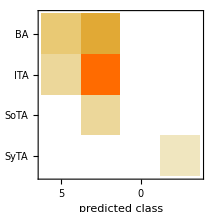
Classifier Measurements
Number of test examples | 55
Accuracy | (76.6.) %
Accuracy baseline | (73.6.) %
-Graphics- |

```mathematica
ClassifierMeasurements[predictedOutput, realOutput]
```

## Testing on a subset of the dataset

Removing some features from the input/training dataset.

```mathematica
sInput = KeyDrop[train, {"id", "epoch", "date", "logo", "timepast", "title", "new"}];
```

```mathematica
sInput = Dataset[sInput];
```

Training the classifier

```mathematica
sClassifier = Classify[sInput->"label"]
```

ClassifierFunction[…]

Removing the same features from the test dataset.

```mathematica
sTest = KeyDrop[test, {"id", "epoch", "date", "logo", "timepast", "title", "new", "label"}];
```

```mathematica
sTest = Dataset[sTest];
```

Running the new classifier on the “cleaned” data.

```mathematica
testPrediction = sClassifier[sTest];
```

```mathematica
testPrediction = StringReplace[testPrediction, {"Interface Technical Architect" -> "ITA", "Business Analyst" -> "BA", "System Technical Architect" -> "SyTA", "Software Technical Architect" -> "SoTA", "Project Manager" -> "PM", "Database Technical Architect" -> "DTA", "Miscellaneous" -> "Misc"}]
```

{ITA,ITA,ITA,ITA,ITA,BA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA,Misc,ITA,BA,ITA,ITA,BA,ITA,ITA,ITA,ITA,BA,ITA,ITA,BA,ITA,BA,ITA,ITA,ITA,ITA,ITA,ITA,BA,ITA,ITA,BA,ITA,ITA,ITA,ITA,ITA,BA,Misc,ITA,ITA,ITA,ITA,ITA,ITA,ITA,ITA}

Testing the accuracy of the classifier

```mathematica
ClassifierMeasurements[testPrediction, realOutput, "Accuracy"]
```

0.781818

Table that makes it easier to decipher the abbreviations.

```mathematica
Grid[{{Style["Abbreviation", Bold],"ITA", "BA", "SyTA", "SoTA", "PM", "DTA", "Misc"}, {Style["Job Label", Bold], "Interface Technical Architect", "Business Analyst", "System Technical Architect", "Software Technical Architect", "Project Manager", "Database Technical Architect", "Miscellaneous"}}, Frame -> All, Alignment->Center, Background-> {{LightGray}, None}]
```

Abbreviation | ITA | BA | SyTA | SoTA | PM | DTA | Misc
Job Label | Interface Technical Architect | Business Analyst | System Technical Architect | Software Technical Architect | Project Manager | Database Technical Architect | Miscellaneous

Confusion matrix of the new classifier.

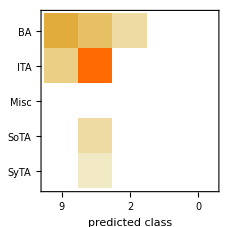
Classifier Measurements
Number of test examples | 55
Accuracy | (78.6.) %
Accuracy baseline | (73.6.) %
-Graphics- |

```mathematica
ClassifierMeasurements[testPrediction, realOutput]
```